```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/shivasankark.a/Documents/Research_work/Tools/PICSHEP/Models/Blazar_U1X

```mathematica
tBH=10^9*365*24*3600;
RS =2.97*10^-6(*pc*);
ri=4*RS;
```

```mathematica
ρc[mχ_,σ_]:=mχ/(σ*10^-26*tBH)(*GeV/cm^3*); 
ρα[α_,r_]:=Num[α]*(1-4 RS/r)^3 r^-α*1/((3.086*10^18)^3);
Num[α_]:=(3.09*10^8*1.988*10^30*5.62*10^26)/(4*π*NIntegrate[(1-4 RS/rr)^3 rr^-α,{rr,ri,10^5 RS}]);
```

```mathematica
ρχ[α_,r_,mχ_,σ_]:=ρα[α,r]*ρc[mχ,σ]/(ρc[mχ,σ]+ρα[α,r]);
```

```mathematica
ρα[7/3,100]//N
```

```mathematica
0.04088874334533763
```

0.0408887

```mathematica
logspace[steps_,min_,max_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)];
rval = N@logspace[100,(*2*10^17*3.24*10^-19*10^-1*)10^-6,10^4];
```

```mathematica
dat1={};
m=10^-6(*GeV*);
Do[
AppendTo[dat1,{rval[[i]],ρχ[3/2,rval[[i]],m,10^-10],ρχ[3/2,rval[[i]],m,0.01],ρχ[3/2,rval[[i]],m,3],ρχ[7/3,rval[[i]],m,10^-10],ρχ[7/3,rval[[i]],m,0.01],ρχ[7/3,rval[[i]],m,3]}],{i,Length[rval]}
]
(*Export["DM_density_mchi=1MeV.txt",dat1,"Table"]; *)
```

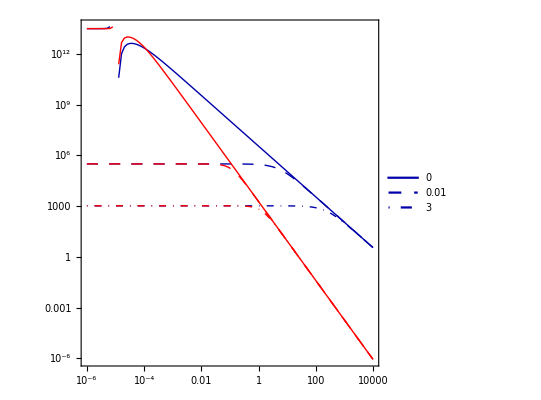

```mathematica
ListLogLogPlot[{dat1[[All,{1,2}]],dat1[[All,{1,3}]],dat1[[All,{1,4}]],dat1[[All,{1,5}]],dat1[[All,{1,6}]],dat1[[All,{1,7}]]},AspectRatio->1,Frame->True,BaseStyle->{FontFamily->"Times",15},FrameStyle->Directive[Black,Thick],PlotRange->(*{{10^-6,10^4},{10^1,10^20}}*)All,PlotStyle->{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Darker[Blue],Thick,DotDashed],Directive[Red,Thick],Directive[Red,Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Red,,Thick,DotDashed]},PlotTheme->"Scientific",Joined->True,PlotRangePadding->None,PlotRangeClipping->False,LabelStyle->Directive[Black,Bold,FontFamily->"Times",18],  PlotLegends->Placed[LineLegend[{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Darker[Blue],Thick,DotDashed],Directive[Red,Thick],Directive[Red,Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Red,,Thick,DotDashed]},{Style["0",25,Black],Style["0.01",25,Black],Style["3",25,Black]},LegendFunction->Framed,LegendLayout->{"Row",2},LegendMargins->{{5,5},{5,5}},LegendMarkerSize->{25},LabelStyle->Directive[Black,Bold,FontFamily->"Times",20]],{{0.98,0.8},{1,1}}]]
```

```mathematica
rmin=2*10^17*3.24*10^-19*0.01;
logspace[steps_,min_,max_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)];
rval = N@logspace[100,rmin,10^10*RS];
dat1={};
m=10^-6(*GeV*);
AbsoluteTiming[Do[
AppendTo[dat1,{rval[[i]],NIntegrate[ρχ[7/3,r,m,10^-8],{r,rmin,rval[[i]]}],NIntegrate[ρχ[7/3,r,m,3],{r,rmin,rval[[i]]}],NIntegrate[ρχ[3/2,r,m,10^-8],{r,rmin,rval[[i]]}],NIntegrate[ρχ[3/2,r,m,3],{r,rmin,rval[[i]]}]}],{i,Length[rval]}
]]
dat1[[All,{2,3,4,5}]] = dat1[[All,{2,3,4,5}]]*3.086*10^18;
Export["DM_Sigma_mchi=1keV.txt",dat1,"Table"];
```

{12.7619,Null}

```mathematica
dat1
```

(0.000648 | 2.86066×10^10 | 707.308 | 8.33009×10^10 | 707.308
0.000774392 | 1.39455×10^25 | 4.12275×10^17 | 4.47211×10^25 | 4.12275×10^17
0.000925436 | 2.54742×10^25 | 9.04963×10^17 | 8.96914×10^25 | 9.04963×10^17
0.00110594 | 3.48779×10^25 | 1.49375×10^18 | 1.34231×10^26 | 1.49375×10^18
0.00132165 | 4.24741×10^25 | 2.19738×10^18 | 1.77745×10^26 | 2.19738×10^18
0.00157944 | 4.85682×10^25 | 3.03825×10^18 | 2.19749×10^26 | 3.03825×10^18
0.00188751 | 5.34333×10^25 | 4.04313×10^18 | 2.59883×10^26 | 4.04313×10^18
0.00225567 | 5.73042×10^25 | 5.24401×10^18 | 2.97899×10^26 | 5.24401×10^18
0.00269563 | 6.03765×10^25 | 6.67912×10^18 | 3.33655×10^26 | 6.67913×10^18
0.00322141 | 6.28108×10^25 | 8.39415×10^18 | 3.67091×10^26 | 8.39416×10^18
0.00384974 | 6.47373×10^25 | 1.04437×10^19 | 3.9821×10^26 | 1.04437×10^19
0.00460063 | 6.62606×10^25 | 1.2893×10^19 | 4.27067×10^26 | 1.2893×10^19
0.00549798 | 6.74643×10^25 | 1.582×10^19 | 4.53747×10^26 | 1.58201×10^19
0.00657035 | 6.8415×10^25 | 1.9318×10^19 | 4.78357×10^26 | 1.9318×10^19
0.00785189 | 6.91656×10^25 | 2.34982×10^19 | 5.01016×10^26 | 2.34982×10^19
0.0093834 | 6.97581×10^25 | 2.84937×10^19 | 5.21849×10^26 | 2.84938×10^19
0.0112136 | 7.02257×10^25 | 3.44636×10^19 | 5.40981×10^26 | 3.44638×10^19
0.0134008 | 7.05947×10^25 | 4.15979×10^19 | 5.58537×10^26 | 4.15982×10^19
0.0160146 | 7.08857×10^25 | 5.01236×10^19 | 5.74635×10^26 | 5.01241×10^19
0.0191383 | 7.11154×10^25 | 6.0312×10^19 | 5.89389×10^26 | 6.0313×10^19
0.0228712 | 7.12965×10^25 | 7.24875×10^19 | 6.02905×10^26 | 7.24893×10^19
0.0273322 | 7.14394×10^25 | 8.70372×10^19 | 6.15283×10^26 | 8.70405×10^19
0.0326633 | 7.15521×10^25 | 1.04424×10^20 | 6.26616×10^26 | 1.0443×10^20
0.0390342 | 7.16409×10^25 | 1.252×10^20 | 6.36991×10^26 | 1.25211×10^20
0.0466478 | 7.1711×10^25 | 1.50026×10^20 | 6.46486×10^26 | 1.50046×10^20
0.0557464 | 7.17663×10^25 | 1.79688×10^20 | 6.55176×10^26 | 1.79724×10^20
0.0666197 | 7.18099×10^25 | 2.15126×10^20 | 6.63128×10^26 | 2.15191×10^20
0.0796138 | 7.18443×10^25 | 2.57459×10^20 | 6.70404×10^26 | 2.57576×10^20
0.0951423 | 7.18714×10^25 | 3.08015×10^20 | 6.77061×10^26 | 3.08228×10^20
0.1137 | 7.18928×10^25 | 3.68374×10^20 | 6.83152×10^26 | 3.6876×10^20
0.135877 | 7.19096×10^25 | 4.40399×10^20 | 6.88724×10^26 | 4.41097×10^20
0.162379 | 7.19229×10^25 | 5.26281×10^20 | 6.93822×10^26 | 5.27544×10^20
0.194051 | 7.19334×10^25 | 6.28569×10^20 | 6.98486×10^26 | 6.30852×10^20
0.231901 | 7.19417×10^25 | 7.50187×10^20 | 7.02753×10^26 | 7.54309×10^20
0.277133 | 7.19482×10^25 | 8.94418×10^20 | 7.06656×10^26 | 9.01845×10^20
0.331187 | 7.19533×10^25 | 1.06481×10^21 | 7.10226×10^26 | 1.07815×10^21
0.395785 | 7.19574×10^25 | 1.26497×10^21 | 7.13493×10^26 | 1.28885×10^21
0.472982 | 7.19606×10^25 | 1.49816×10^21 | 7.1648×10^26 | 1.54064×10^21
0.565237 | 7.19631×10^25 | 1.76662×10^21 | 7.19214×10^26 | 1.84153×10^21
0.675486 | 7.19651×10^25 | 2.07057×10^21 | 7.21714×10^26 | 2.2011×10^21
0.807238 | 7.19667×10^25 | 2.40703×10^21 | 7.24002×10^26 | 2.63078×10^21
0.964689 | 7.19679×10^25 | 2.76875×10^21 | 7.26094×10^26 | 3.14424×10^21
1.15285 | 7.19689×10^25 | 3.14405×10^21 | 7.28008×10^26 | 3.7578×10^21
1.37771 | 7.19696×10^25 | 3.51797×10^21 | 7.29759×10^26 | 4.49096×10^21
1.64643 | 7.19703×10^25 | 3.87499×10^21 | 7.3136×10^26 | 5.36702×10^21
1.96757 | 7.19707×10^25 | 4.20211×10^21 | 7.32826×10^26 | 6.41377×10^21
2.35134 | 7.19711×10^25 | 4.49096×10^21 | 7.34166×10^26 | 7.66441×10^21
2.80997 | 7.19714×10^25 | 4.73833×10^21 | 7.35392×10^26 | 9.15857×10^21
3.35805 | 7.19716×10^25 | 4.94514×10^21 | 7.36513×10^26 | 1.09435×10^22
4.01303 | 7.19718×10^25 | 5.11499×10^21 | 7.37539×10^26 | 1.30755×10^22
4.79577 | 7.1972×10^25 | 5.25268×10^21 | 7.38478×10^26 | 1.56217×10^22
5.73118 | 7.19721×10^25 | 5.36332×10^21 | 7.39336×10^26 | 1.8662×10^22
6.84904 | 7.19722×10^25 | 5.45166×10^21 | 7.40121×10^26 | 2.22914×10^22
8.18494 | 7.19722×10^25 | 5.52191×10^21 | 7.4084×10^26 | 2.66225×10^22
9.78141 | 7.19723×10^25 | 5.57761×10^21 | 7.41497×10^26 | 3.17888×10^22
11.6893 | 7.19723×10^25 | 5.6217×10^21 | 7.42098×10^26 | 3.79479×10^22
13.9692 | 7.19724×10^25 | 5.65655×10^21 | 7.42648×10^26 | 4.52851×10^22
16.6939 | 7.19724×10^25 | 5.68407×10^21 | 7.43151×10^26 | 5.40175×10^22
19.95 | 7.19724×10^25 | 5.7058×10^21 | 7.43611×10^26 | 6.43976×10^22
23.8413 | 7.19725×10^25 | 5.72294×10^21 | 7.44032×10^26 | 7.67167×10^22
28.4915 | 7.19725×10^25 | 5.73647×10^21 | 7.44417×10^26 | 9.1307×10^22
34.0487 | 7.19725×10^25 | 5.74714×10^21 | 7.44769×10^26 | 1.08542×10^23
40.6899 | 7.19725×10^25 | 5.75555×10^21 | 7.45091×10^26 | 1.28833×10^23
48.6264 | 7.19725×10^25 | 5.76219×10^21 | 7.45386×10^26 | 1.5262×10^23
58.1109 | 7.19725×10^25 | 5.76742×10^21 | 7.45656×10^26 | 1.80357×10^23
69.4454 | 7.19725×10^25 | 5.77155×10^21 | 7.45902×10^26 | 2.12487×10^23
82.9907 | 7.19725×10^25 | 5.7748×10^21 | 7.46128×10^26 | 2.49404×10^23
99.1779 | 7.19725×10^25 | 5.77737×10^21 | 7.46334×10^26 | 2.91407×10^23
118.522 | 7.19725×10^25 | 5.77939×10^21 | 7.46523×10^26 | 3.38647×10^23
141.64 | 7.19725×10^25 | 5.78098×10^21 | 7.46696×10^26 | 3.91068×10^23
169.267 | 7.19725×10^25 | 5.78224×10^21 | 7.46854×10^26 | 4.4837×10^23
202.282 | 7.19725×10^25 | 5.78323×10^21 | 7.46998×10^26 | 5.09986×10^23
241.737 | 7.19725×10^25 | 5.78402×10^21 | 7.4713×10^26 | 5.75098×10^23
288.888 | 7.19725×10^25 | 5.78463×10^21 | 7.47251×10^26 | 6.42694×10^23
345.235 | 7.19725×10^25 | 5.78512×10^21 | 7.47362×10^26 | 7.11651×10^23
412.573 | 7.19725×10^25 | 5.7855×10^21 | 7.47463×10^26 | 7.80833×10^23
493.044 | 7.19725×10^25 | 5.78581×10^21 | 7.47556×10^26 | 8.49183×10^23
589.212 | 7.19725×10^25 | 5.78604×10^21 | 7.4764×10^26 | 9.15789×10^23
704.137 | 7.19725×10^25 | 5.78623×10^21 | 7.47718×10^26 | 9.79923×10^23
841.479 | 7.19725×10^25 | 5.78638×10^21 | 7.47789×10^26 | 1.04105×10^24
1005.61 | 7.19725×10^25 | 5.7865×10^21 | 7.47853×10^26 | 1.09883×10^24
1201.75 | 7.19725×10^25 | 5.78659×10^21 | 7.47913×10^26 | 1.15306×10^24
1436.15 | 7.19725×10^25 | 5.78666×10^21 | 7.47967×10^26 | 1.20369×10^24
1716.27 | 7.19725×10^25 | 5.78672×10^21 | 7.48017×10^26 | 1.25073×10^24
2051.03 | 7.19725×10^25 | 5.78677×10^21 | 7.48062×10^26 | 1.29429×10^24
2451.08 | 7.19725×10^25 | 5.7868×10^21 | 7.48104×10^26 | 1.33451×10^24
2929.16 | 7.19725×10^25 | 5.78683×10^21 | 7.48141×10^26 | 1.37158×10^24
3500.49 | 7.19725×10^25 | 5.78685×10^21 | 7.48176×10^26 | 1.40567×10^24
4183.25 | 7.19725×10^25 | 5.78687×10^21 | 7.48208×10^26 | 1.437×10^24
4999.19 | 7.19725×10^25 | 5.78688×10^21 | 7.48237×10^26 | 1.46575×10^24
5974.28 | 7.19725×10^25 | 5.78689×10^21 | 7.48264×10^26 | 1.49212×10^24
7139.55 | 7.19725×10^25 | 5.7869×10^21 | 7.48288×10^26 | 1.51629×10^24
8532.12 | 7.19725×10^25 | 5.78691×10^21 | 7.4831×10^26 | 1.53843×10^24
10196.3 | 7.19725×10^25 | 5.78691×10^21 | 7.48331×10^26 | 1.5587×10^24
12185.1 | 7.19725×10^25 | 5.78692×10^21 | 7.48349×10^26 | 1.57727×10^24
14561.8 | 7.19725×10^25 | 5.78692×10^21 | 7.48366×10^26 | 1.59426×10^24
17402. | 7.19725×10^25 | 5.78692×10^21 | 7.48382×10^26 | 1.60981×10^24
20796.3 | 7.19725×10^25 | 5.78693×10^21 | 7.48396×10^26 | 1.62405×10^24
24852.5 | 7.19725×10^25 | 5.78693×10^21 | 7.48409×10^26 | 1.63707×10^24
29700. | 7.19725×10^25 | 5.78693×10^21 | 7.48421×10^26 | 1.64899×10^24)

```mathematica
{{29700.00000000002, 7.197251489491541*^25, 1.5004935585973436*^23, 5.786928807067365*^21, 7.484210281808379*^26, 1.1766836407001848*^25, 1.6489877859363483*^24}}
```

```mathematica
{{2.2724066564646837*^25, 1.5004935585973436*^23, 5.786928807067365*^21, 2.4961818666810035*^26, 1.1766836407001848*^25, 1.6489877859363483*^24}}
```

```mathematica
{{2.0290527761301458*^24, 1.5004935585973436*^23, 5.786928807067365*^21, 5.5020180764915385*^25, 1.1766836407001848*^25, 1.6489877859363483*^24}}
```

```mathematica
dat1[[All,{2,3,4,5,6,7}]] = dat1[[All,{2,3,4,5,6,7}]]*10^2;
```

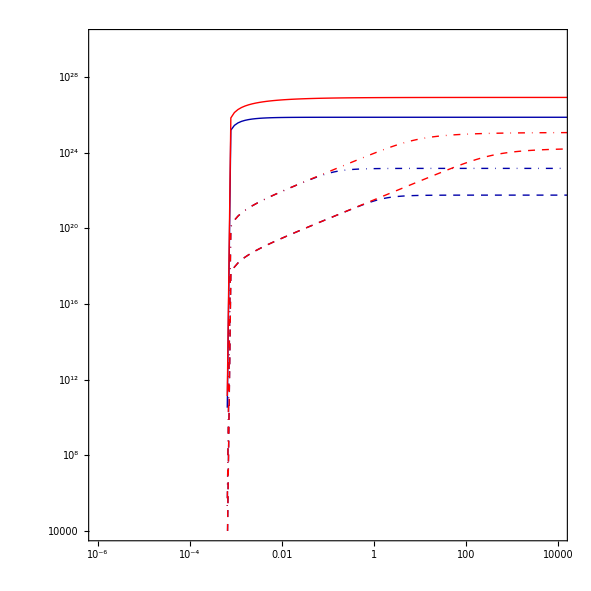

```mathematica
A=ListLogLogPlot[{dat1[[All,{1,2}]],dat1[[All,{1,3}]],dat1[[All,{1,4}]],dat1[[All,{1,5}]],dat1[[All,{1,6}]],dat1[[All,{1,7}]]},AspectRatio->1,Frame->True,BaseStyle->{FontFamily->"Times",15},FrameStyle->Directive[Black,Thick],PlotRange->{{10^-6,10^4},{10^4,10^30}},PlotStyle->{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,DotDashed],Directive[Darker[Blue],Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,DotDashed],Directive[Red,Thick,Dashed]},PlotTheme->"Scientific",Joined->True,PlotRangePadding->None,PlotRangeClipping->False,LabelStyle->Directive[Black,Bold,FontFamily->"Times",18](*,  PlotLegends->Placed[LineLegend[{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Darker[Blue],Thick,DotDashed],Directive[Red,Thick],Directive[Red,Thick,Dashing[{0.02,0.02,0.02,0.02,0.02}]],Directive[Red,,Thick,DotDashed]},{Style["0",25,Black],Style["0.01",25,Black],Style["3",25,Black]},LegendFunction->Framed,LegendLayout->{"Row",2},LegendMargins->{{5,5},{5,5}},LegendMarkerSize->{25},LabelStyle->Directive[Black,Bold,FontFamily->"Times",20]],{{0.98,0.8},{1,1}}]*)]
```

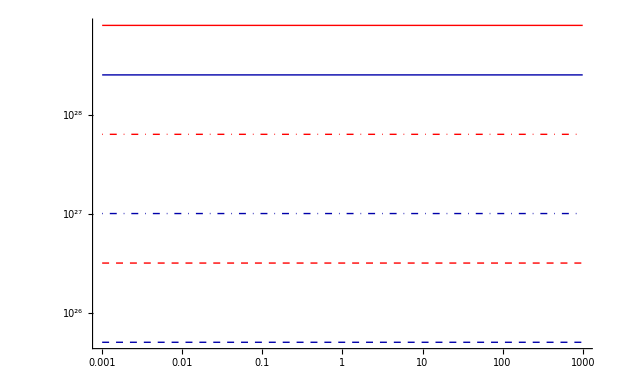

```mathematica
Bplot=LogLogPlot[{10^31.4*(10^-3/10^-3)^(1-1)*10^-3,10^30.0*(10^-3/10^-3)^(1-0.48)*10^-3,10^28.7*(10^-3/10^-3)^(1-0.43)*10^-3,10^31.9*(10^-3/10^-3)^(1-1)*10^-3,10^30.8*(10^-3/10^-3)^(1-0.73)*10^-3,10^29.5*(10^-3/10^-3)^(1-0.66)*10^-3},{x,10^-3,10^3},PlotStyle->{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,DotDashed],Directive[Darker[Blue],Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,DotDashed],Directive[Red,,Thick,Dashed]}]
```

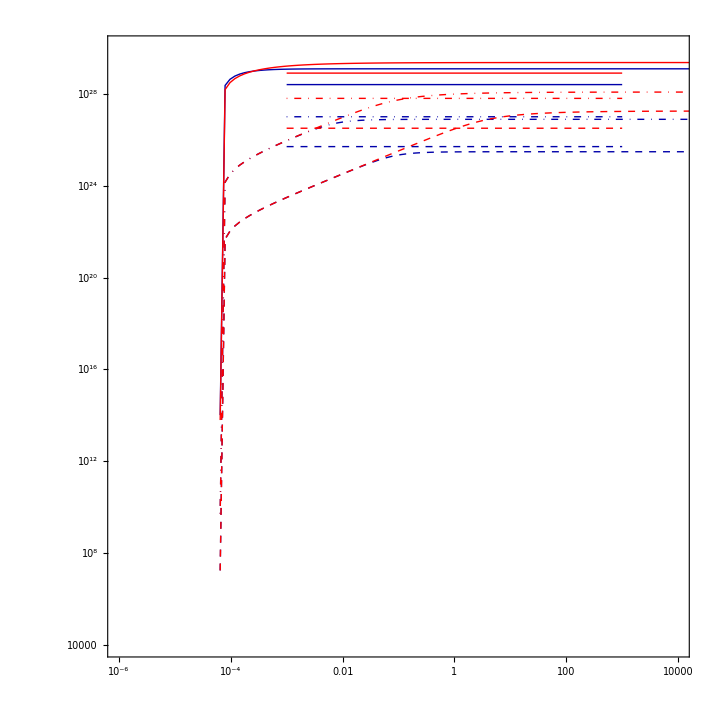

```mathematica
Show[A,Bplot]
```

```mathematica
(*Σ/mχ vs mχ*)
rmin=2*10^17*3.24*10^-19;
logspace[steps_,min_,max_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)];
m =  N@logspace[200,10^-6,10^3];
rval = 10^5;
dat1={};
AbsoluteTiming[Do[
AppendTo[dat1,{m[[i]],NIntegrate[ρχ[7/3,r,m[[i]],10^-8],{r,rmin,rval}],NIntegrate[ρχ[7/3,r,m[[i]],3],{r,rmin,rval}],NIntegrate[ρχ[3/2,r,m[[i]],10^-8],{r,rmin,rval}],NIntegrate[ρχ[3/2,r,m[[i]],3],{r,rmin,rval}]}],{i,Length[m]}
]]
dat1[[All,{2,3,4,5}]] = dat1[[All,{2,3,4,5}]]*3.086*10^18/m;
Export["Sigmamchi_vs_mchi.txt",dat1,"Table"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.86352}. NIntegrate obtained 4253.76 and 0.00519367 for the integral and error estimates.

{28.4751,Null}

Sigmamchi_vs_mchi.txt

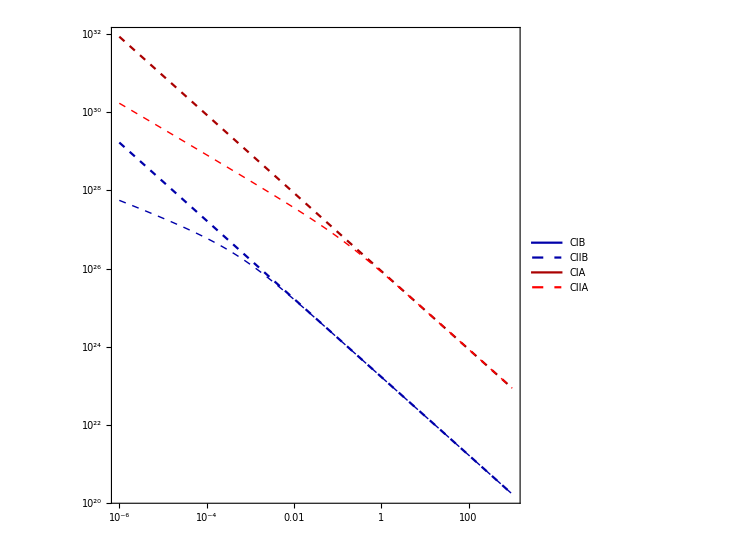

```mathematica
Cplot=ListLogLogPlot[{dat1[[All,{1,2}]],dat1[[All,{1,3}]],dat1[[All,{1,4}]],dat1[[All,{1,5}]]},AspectRatio->1,Frame->True,BaseStyle->{FontFamily->"Times",15},FrameStyle->Directive[Black,Thick],PlotRange->(*{{10^-6,10^4},{10^20,10^34}}*)All,PlotStyle->{Directive[Darker[Blue],Dashed],Directive[Darker[Blue],Thick,Dashed],Directive[Darker[Red],Dashed],Directive[Red,Thick,Dashed]},PlotTheme->"Scientific",Joined->True,PlotRangePadding->None,PlotRangeClipping->False,LabelStyle->Directive[Black,Bold,FontFamily->"Times",18],  PlotLegends->Placed[LineLegend[{Directive[Darker[Blue],Thick],Directive[Darker[Blue],Thick,Dashed],Directive[Darker[Red],Thick],Directive[Red,Thick,Dashed]},{Style["CIB",25,Black],Style["CIIB",25,Black],Style["CIA",25,Black],Style["CIIA",25,Black]},LegendFunction->Framed,LegendLayout->{"Row",2},LegendMargins->{{5,5},{5,5}},LegendMarkerSize->{25},LabelStyle->Directive[Black,Bold,FontFamily->"Times",20]],{{0.98,0.95},{1,1}}]]
```

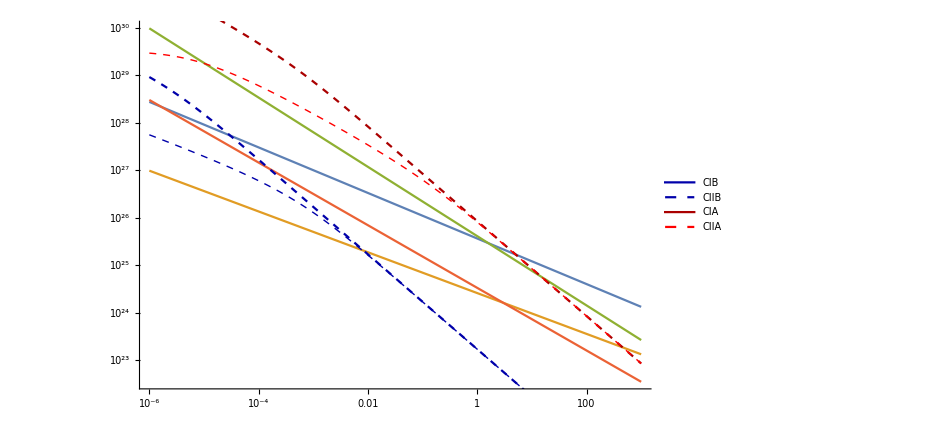

```mathematica
Show[Bplot,Cplot]
```